```mathematica
<<Combinatorica`
<<GraphUtilities`
Needs["MATLink`"]
OpenMATLAB[]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

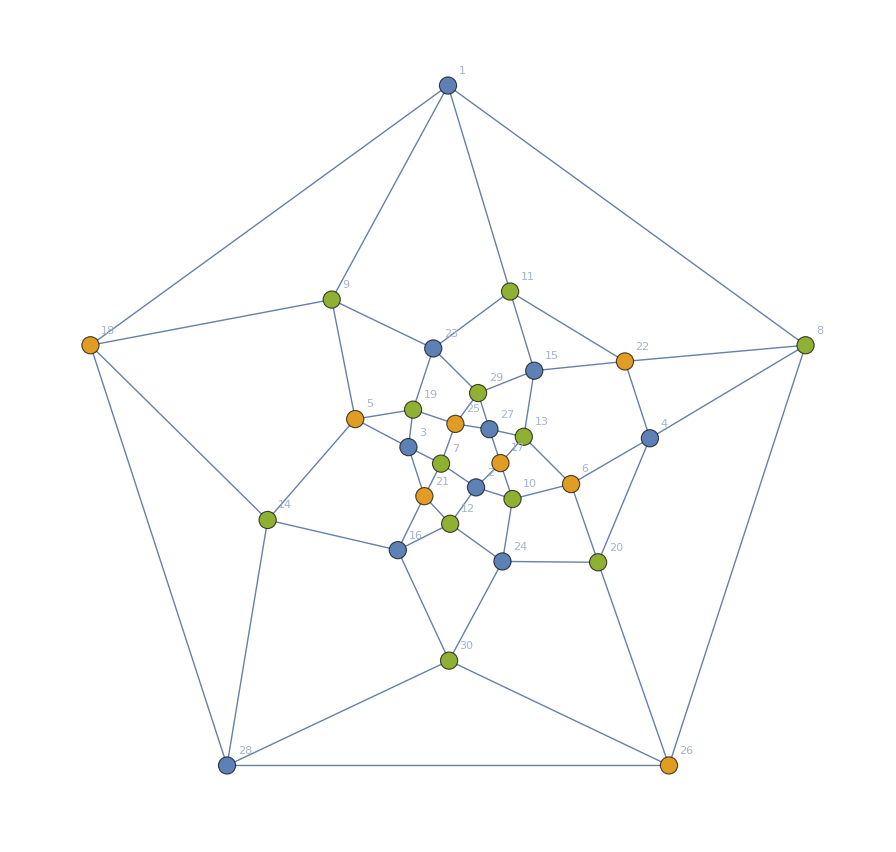

```mathematica
Clear[g,AdjacencyMat,Matrix];
MEvaluate["mat = Great_Circles_Problem_3D;"]; AdjacencyMat = IntegerPart[MGet["mat"]];
g=AdjacencyGraph[AdjacencyMat,GraphLayout->"TutteEmbedding",VertexLabels->Array[#->#&,Length@AdjacencyMat], VertexSize->0.5];
mvc=MinimumVertexColoring@ToCombinatoricaGraph[g];
GColored1=SetProperty[g,System`VertexStyle->Thread[System`VertexList[g]->(ColorData[97]/@mvc)]]
```

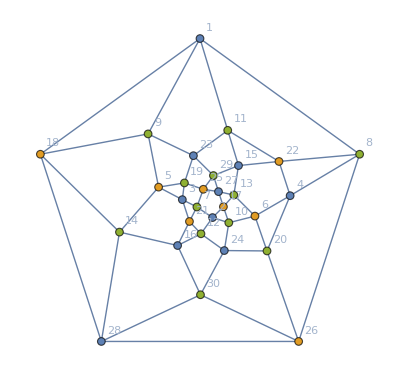

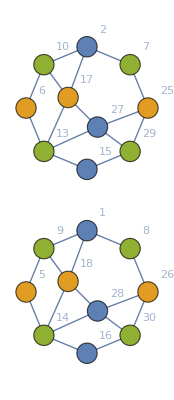

```mathematica
g1=GColored1
g11=VertexDelete[g1,{11,22,4,20,24,12,21,3,19,23}]
```

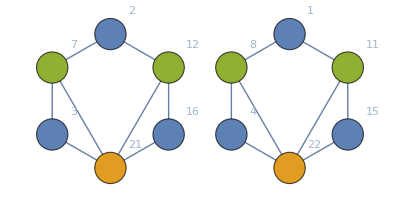

```mathematica
g12=VertexDelete[g11,{18,9,23,29,17,10,24,30}]
```